```mathematica
ClearAll["Global`*"];
$HistoryLength=0;
```

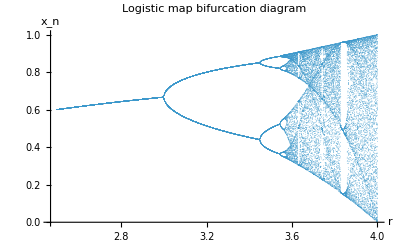

```mathematica
u=1.0;    
mu=1.0;
a=1.4;
b=1.4;
x0=0.2;
y0=0.1;
z0=0.0;

alphaVal=1.4;
betaVal=1.4;
deltaVal=1.2;
epsVal=0.25;
gammaVal=0.9;

C0=u/mu;
S0=(a/b) C0;

(* Logistic map*)
logisticStep[r_?NumericQ][x_?NumericQ]:=r*x*(1-x);

logisticOrbit[r_?NumericQ,x0_?NumericQ,n_Integer?NonNegative]:=NestList[logisticStep[r],x0,n];

(*Logistic bifurcation data:r vs last nKeep values*)
logisticBifurcationData[rmin_?NumericQ,rmax_?NumericQ,nR_Integer?Positive,nTransient_Integer?NonNegative,nKeep_Integer?Positive,x0_?NumericQ]:=Module[{rs,orbit,keep},rs=Subdivide[rmin,rmax,nR];
Flatten[Table[orbit=logisticOrbit[r,x0,nTransient+nKeep];
keep=orbit[[-nKeep;;]];
Transpose[{ConstantArray[r,nKeep],keep}],{r,rs}],1]];

(*Logistic Lyapunov exponent*)
logisticLyapunov[r_?NumericQ,x0_?NumericQ,nTransient_Integer?NonNegative,n_Integer?Positive]:=Module[{orbit,keep,deriv},orbit=logisticOrbit[r,x0,nTransient+n];
keep=orbit[[-n;;]];
deriv=Abs[r*(1-2*keep)];
Mean[Log[deriv+10^-30]] ];

rForBif=3.9;
x0Log=0.213;

bifData=logisticBifurcationData[2.5,4.0,900,600,60,x0Log];
pLogisticBif=ListPlot[bifData,PlotRange->All,PlotStyle->PointSize[0.001],AxesLabel->{"r","x_n"},PlotLabel->"Logistic map bifurcation diagram"];
pLogisticBif
```

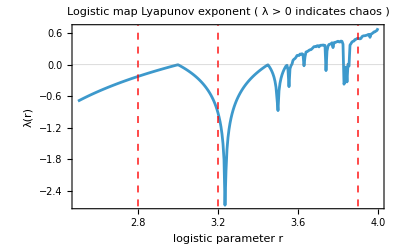

```mathematica
(*Logistic map Lyapunov exponent λ(r)*)

logisticLyapunov[r_?NumericQ,x0_?NumericQ,nTransient_Integer,nIter_Integer]:=Module[{x=x0,sum=0.,i,deriv},(*discard transient*)Do[x=r x (1-x),{i,nTransient}];
(*accumulate log|f'(x)|*)Do[x=r x (1-x);
deriv=Abs[r (1-2 x)];
(*avoid Log[0] if x hits exactly 0.5 etc.*)sum+=Log[Max[deriv,10^-12]];,{i,nIter}];
sum/nIter];

(*scan r*)
rMin=2.5;rMax=4.0;rStep=0.005;
x0Log=0.2;          (*keep consistent with your logistic seed*)
nTransient=800;
nIter=2000;

lyapData=Table[{r,logisticLyapunov[r,x0Log,nTransient,nIter]},{r,rMin,rMax,rStep}];

pLyap=ListLinePlot[lyapData,Frame->True,FrameLabel->{"logistic parameter r","λ(r)"},PlotRange->{{rMin,rMax},All},GridLines->{None,{0}},PlotLabel->"Logistic map Lyapunov exponent ( λ > 0 indicates chaos )",Epilog->{(*mark your three example r values*){Red,Dashed,Line[{{2.8,-10},{2.8,10}}]},{Red,Dashed,Line[{{3.2,-10},{3.2,10}}]},{Red,Dashed,Line[{{3.9,-10},{3.9,10}}]},{Red,Text[Style["r=2.8",12],{2.8,0.8}]},{Red,Text[Style["r=3.2",12],{3.2,0.8}]},{Red,Text[Style["r=3.9",12],{3.9,0.8}]}}];

pLyap
```

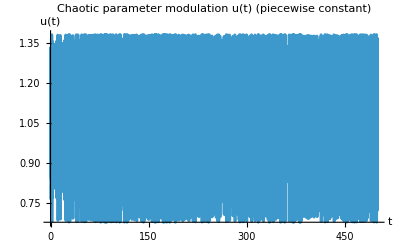

```mathematica
tMax=500;       (*total simulated time for ODE*)
Tstep=0.2;       (*how often the discrete map updates*)
nSteps=Ceiling[tMax/Tstep]+2;

(*Logistic parameter r*)
rLog=3.9;
(*amplitude of modulation*)
uAmp=0.8;  

xSeq=logisticOrbit[rLog,x0Log,nSteps];  
uSeq=u*(1+uAmp*(xSeq-0.5));  

(*piecewise-constant function u(t)*)
uFunc[t_?NumericQ]:=Module[{k=Floor[t/Tstep]+1},uSeq[[Clip[k,{1,Length[uSeq]}]]]];

pU=Plot[uFunc[t],{t,0,tMax},PlotRange->All,AxesLabel->{"t","u(t)"},PlotLabel->"Chaotic parameter modulation u(t) (piecewise constant)"];
pU
```

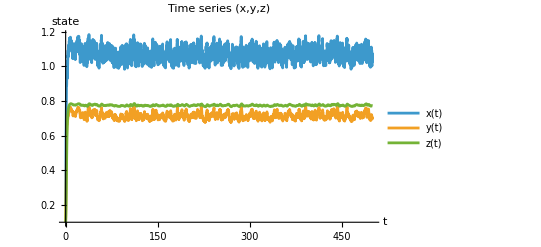

```mathematica
eqsPhase3:={x'[t]==uFunc[t]-x[t],y'[t]==alphaVal*x[t]-betaVal*y[t]-gammaVal*y[t]*z[t],z'[t]==deltaVal*y[t]*(1-z[t])-epsVal*z[t]};

(*Initial conditions*)
ics={x[0]==0.2,y[0]==0.1,z[0]==0.1};

solvePhase3[acc_:12,prec_:12,maxStep_:Automatic]:=Module[{opts},opts={Method->{"StiffnessSwitching"},MaxSteps->Infinity,AccuracyGoal->acc,PrecisionGoal->prec};(*Use StiffnessSwitching to handle numerical stiffness caused by jump discontinuities in the chaotic driver u(t)*)
If[maxStep=!=Automatic,AppendTo[opts,MaxStepSize->maxStep]];
NDSolveValue[Join[eqsPhase3,ics],{x,y,z},{t,0,tMax},Sequence@@opts]];


sol=solvePhase3[12,12,Automatic];

xSol[t_?NumericQ]:=sol[[1]][t];
ySol[t_?NumericQ]:=sol[[2]][t];
zSol[t_?NumericQ]:=sol[[3]][t];

(*Time series*)
pTS=Plot[Evaluate[{xSol[t],ySol[t],zSol[t]}],{t,0,tMax},PlotRange->All,AxesLabel->{"t","state"},PlotLabel->"Time series (x,y,z)",PlotLegends->{"x(t)","y(t)","z(t)"}];
pTS
```

```mathematica
(*3D trajectory (discard transient)*)
tTransient=20;
p3D=ParametricPlot3D[Evaluate[{xSol[t],ySol[t],zSol[t]}],{t,tTransient,tMax},PlotRange->All,BoxRatios->{1,1,1},PlotRangePadding->Scaled[0.05],AxesLabel->{"x","y","z"},ViewPoint->{2.2,-2.4,1.3},PlotLabel->"3D phase trajectory"];
p3D
```

-Graphics3D-

```mathematica
(*Stroboscopic sampling*)
nStart=Ceiling[tTransient/Tstep];
nEnd=Floor[tMax/Tstep];

samples=Table[{xSol[n*Tstep],ySol[n*Tstep],zSol[n*Tstep]},{n,nStart,nEnd}];

pStrobe3D=ListPointPlot3D[samples,PlotRange->All,BoxRatios->{1,1,1},PlotRangePadding->Scaled[0.05],AxesLabel->{"x","y","z"},ViewPoint->{2.2,-2.4,1.3},PlotLabel->"Stroboscopic samples"];
pStrobe3D
```

-Graphics3D-

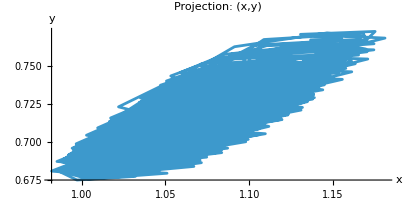

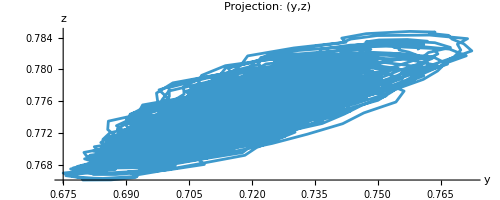

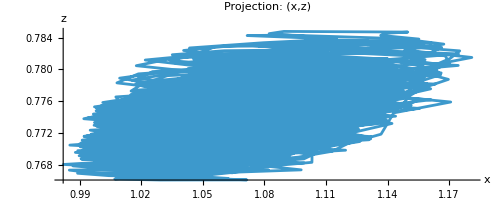

```mathematica
pXY=ParametricPlot[Evaluate[{xSol[t],ySol[t]}],{t,tTransient,tMax},PlotRange->All,AxesLabel->{"x","y"},PlotLabel->"Projection: (x,y)"];

pYZ=ParametricPlot[Evaluate[{ySol[t],zSol[t]}],{t,tTransient,tMax},PlotRange->All,AxesLabel->{"y","z"},PlotLabel->"Projection: (y,z)"];

pXZ=ParametricPlot[Evaluate[{xSol[t],zSol[t]}],{t,tTransient,tMax},PlotRange->All,AxesLabel->{"x","z"},PlotLabel->"Projection: (x,z)"];

pXY
pYZ
pXZ
```

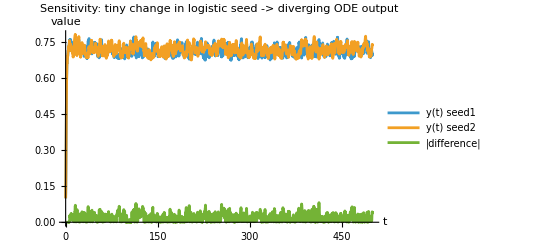

```mathematica
(*Sensitivity to logistic initial condition*)
x0Log2=x0Log+10^-8;
xSeq2=logisticOrbit[rLog,x0Log2,nSteps];
uSeq2=u*(1+uAmp*(xSeq2-0.5));

uFunc2[t_?NumericQ]:=Module[{k=Floor[t/Tstep]+1},uSeq2[[Clip[k,{1,Length[uSeq2]}]]]];

eqsPhase3b:={x'[t]==uFunc2[t]-x[t],y'[t]==alphaVal*x[t]-betaVal*y[t]-gammaVal*y[t]*z[t],z'[t]==deltaVal*y[t]*(1-z[t])-epsVal*z[t]};

sol2=NDSolveValue[Join[eqsPhase3b,ics],{x,y,z},{t,0,tMax},Method->{"StiffnessSwitching"},MaxSteps->Infinity,AccuracyGoal->12,PrecisionGoal->12];

ySol2[t_?NumericQ]:=sol2[[2]][t];

pSens=Plot[Evaluate[{ySol[t],ySol2[t],Abs[ySol[t]-ySol2[t]]}],{t,0,tMax},PlotRange->All,AxesLabel->{"t","value"},PlotLegends->{"y(t) seed1","y(t) seed2","|difference|"},PlotLabel->"Sensitivity: tiny change in logistic seed -> diverging ODE output"];
pSens
```

```mathematica
(*Numerical robustness check*)
```

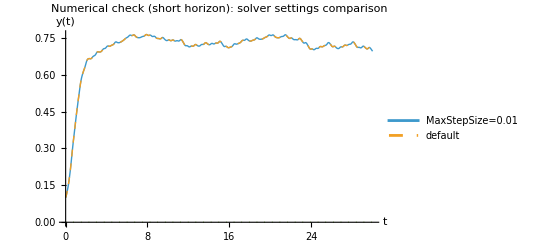

```mathematica
solFine=solvePhase3[12,12,0.01];
yFine[t_?NumericQ]:=solFine[[2]][t];

tCheck=30;
pNumCheck=Plot[{yFine[t],ySol[t],Abs[ySol[t]-yFine[t]]},{t,0,tCheck},PlotStyle->{Directive[Thick],Directive[Thick,Dashed],Directive[Thin,Dotted]},PlotLegends->{"MaxStepSize=0.01","default"},PlotLabel->"Numerical check (short horizon): solver settings comparison",AxesLabel->{"t","y(t)"}];
pNumCheck
```

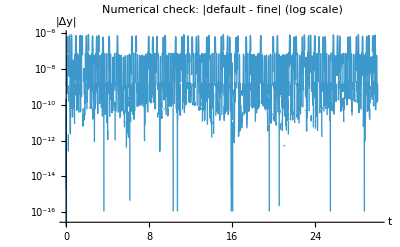

```mathematica
pNumCheckDiffLog=Plot[Abs[ySol[t]-yFine[t]],{t,0,tCheck},ScalingFunctions->{"Linear","Log"},PlotRange->All,PlotStyle->{Directive[Thick]},PlotLabel->"Numerical check: |default - fine| (log scale)",AxesLabel->{"t","|Δy|"}];
pNumCheckDiffLog
```

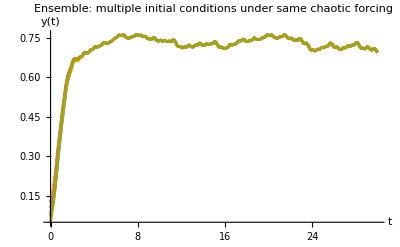

```mathematica
(*Ensemble of ODE initial conditions (same forcing)*)
SeedRandom[42];
icsList=Table[{x[0]==RandomReal[{0.15,0.25}],y[0]==RandomReal[{0.05,0.15}],z[0]==RandomReal[{0.05,0.15}]},{10}];

solEnsemble=Table[NDSolveValue[Join[eqsPhase3,ic],{x,y,z},{t,0,tMax},Method->{"StiffnessSwitching"},MaxSteps->Infinity,AccuracyGoal->10,PrecisionGoal->10],{ic,icsList}];

pEns=Plot[Evaluate@Table[solEnsemble[[i,2]][t],{i,Length[solEnsemble]}],{t,0,tCheck},PlotRange->All,AxesLabel->{"t","y(t)"},PlotLabel->"Ensemble: multiple initial conditions under same chaotic forcing"];
pEns
```

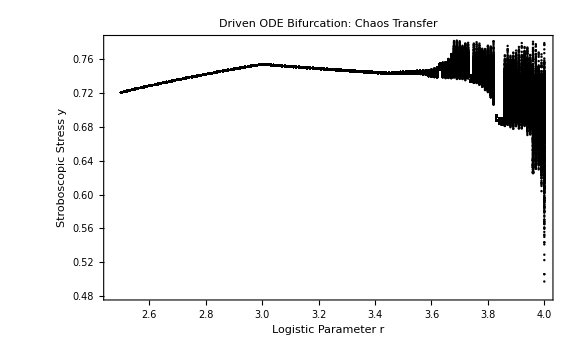

```mathematica
(*Driven ODE Bifurcation*)
Clear[logisticOrbitSafe];
logisticOrbitSafe[r_,xStart_,drop_,n_]:=Drop[RecurrenceTable[{x[i+1]==r x[i] (1-x[i]),x[0]==xStart},x,{i,0,n+drop}],drop];

(*Scan parameters*)
rScanList=Range[2.5,4.0,0.01];
tMaxBif=400;
dropBif=200;
nStepsBif=Floor[tMaxBif/Tstep]+10;

Clear[getStrobeY];
getStrobeY[r_?NumericQ]:=Module[{xSeq,uSeq,uFuncLocal,sol,yVals,sampleTimes},xSeq=logisticOrbitSafe[r,x0Log,dropBif,nStepsBif];
uSeq=u*(1+uAmp*(xSeq-0.5));
uFuncLocal[t_?NumericQ]:=uSeq[[Clip[Floor[t/Tstep]+1,{1,Length[uSeq]}]]];
(*Solve ODE*)sol=Check[NDSolveValue[{x'[t]==uFuncLocal[t]-x[t],y'[t]==alphaVal*x[t]-betaVal*y[t]-gammaVal*y[t]*z[t],z'[t]==deltaVal*y[t]*(1-z[t])-epsVal*z[t],x[0]==x0,y[0]==y0,z[0]==z0},y,{t,0,tMaxBif},Method->{"StiffnessSwitching"},MaxSteps->Infinity],$Failed ];
If[sol===$Failed,{},sampleTimes=Range[tMaxBif/2,tMaxBif,Tstep];
yVals=sol/@sampleTimes;
Thread[{r,yVals}]]];
dataBif=Flatten[Monitor[Table[getStrobeY[r],{r,rScanList}],r],1];

ListPlot[dataBif,PlotRange->All,PlotStyle->{Black,PointSize[0.003]},PlotLabel->"Driven ODE Bifurcation: Chaos Transfer",AxesLabel->{"Logistic Parameter r","Stroboscopic Stress y"},ImageSize->Large,PlotTheme->"Scientific"]
```

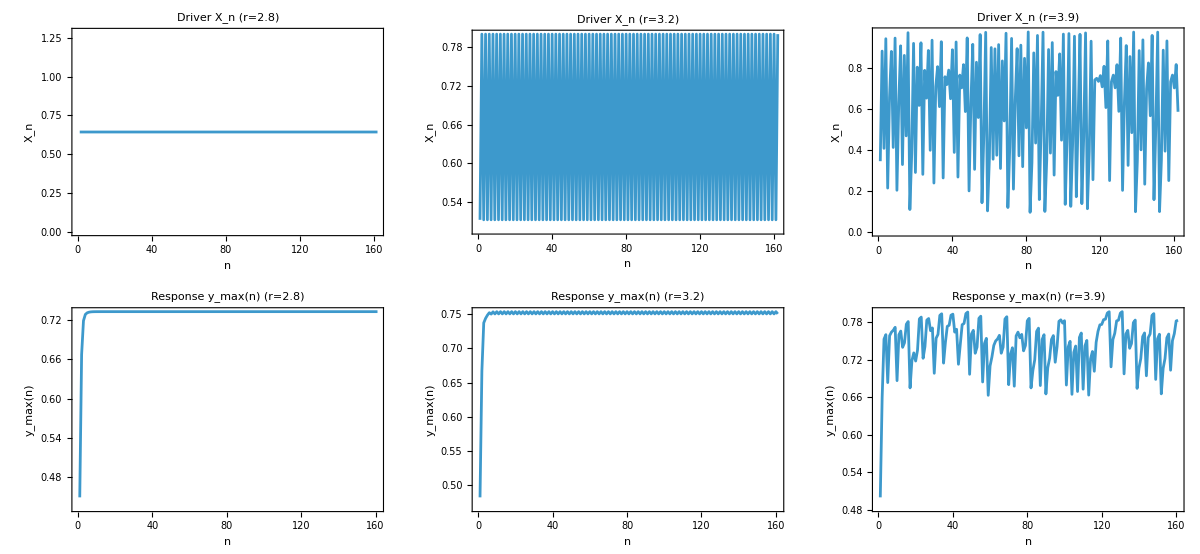

```mathematica
(*2×3 panels:X_n and y_max(n) in stable/period-2/chaotic regimes*)
ubase=1.0;
A=0.7;
Tstep=1.0;      
nTotal=220;      
nTransient=60;       
samplesPerStep=60;   
x0ODE=0.2;y0ODE=0.1;z0ODE=0.0;

logisticSeq[r_,x0_,n_]:=NestList[r # (1-#)&,x0,n];

uFromX[x_]:=ubase+A*(x-1/2);

uStepFun[uSeq_,T_]:=Module[{tgrid},tgrid=Range[0,Length[uSeq]-1]*T;
Interpolation[Transpose[{tgrid,uSeq}],InterpolationOrder->0]];

simulateYmaxFromDriver[uSeq_]:=Module[{uStep,tMax,sol,xSol,ySol,zSol,yMaxList,t1,t2,ts,ys},uStep=uStepFun[uSeq,Tstep];
tMax=(Length[uSeq]-1)*Tstep;
sol=NDSolveValue[{x'[t]==uStep[t]-x[t],y'[t]==alphaVal x[t]-betaVal y[t]-gammaVal y[t] z[t],z'[t]==deltaVal y[t] (1-z[t])-epsVal z[t],x[0]==x0ODE,y[0]==y0ODE,z[0]==z0ODE},{x,y,z},{t,0,tMax}];
xSol=sol[[1]];ySol=sol[[2]];zSol=sol[[3]];
(*每个 step 取一次 y_max*)yMaxList=Table[t1=(k-1)*Tstep;t2=k*Tstep;
ts=Subdivide[t1,t2,samplesPerStep];
ys=ySol/@ts;
Max[ys],{k,1,Length[uSeq]-1}];
<|"xSol"->xSol,"ySol"->ySol,"zSol"->zSol,"yMax"->yMaxList|>];

rList={2.8,3.2,3.9};  (*stable/period-2/chaotic*)

results=Table[xSeq=logisticSeq[r,x0Log,nTotal];
xSeqKeep=xSeq[[nTransient;;-1]];
uSeqKeep=uFromX/@xSeqKeep;
sim=simulateYmaxFromDriver[uSeqKeep];
<|"r"->r,"xSeq"->xSeqKeep,"yMax"->sim["yMax"]|>,{r,rList}];

xPanels=Table[ListLinePlot[Transpose[{Range[1,Length[results[[i,"xSeq"]]]],results[[i,"xSeq"]]}],Frame->True,FrameLabel->{"n","X_n"},PlotLabel->"Driver X_n (r="<>ToString[results[[i,"r"]]]<>")",PlotRange->All,ImageSize->300],{i,Length[results]}];

yPanels=Table[ListLinePlot[Transpose[{Range[1,Length[results[[i,"yMax"]]]],results[[i,"yMax"]]}],Frame->True,FrameLabel->{"n","y_max(n)"},PlotLabel->"Response y_max(n) (r="<>ToString[results[[i,"r"]]]<>")",PlotRange->All,ImageSize->300],{i,Length[results]}];

pPanels=GraphicsGrid[{xPanels,yPanels},Spacings->{0.6,0.8}];
pPanels
```

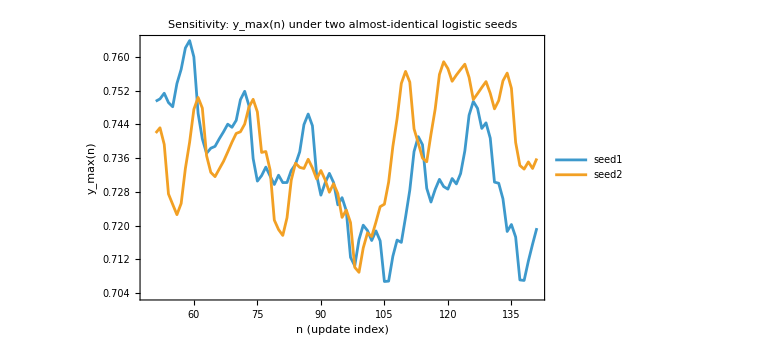

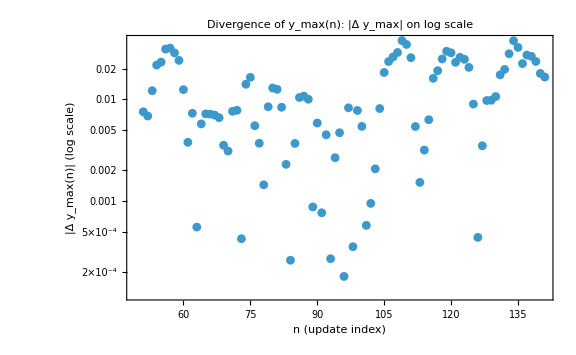

```mathematica
(* Build y_max(n) sequences from two trajectories*)
ClearAll["Global`*"];
$HistoryLength=0;
alphaVal=1.4;
betaVal=1.4;
gammaVal=0.9;
deltaVal=1.2;
epsVal=0.25;

rChaotic=3.9; 
tMax=500;     
Tstep=0.2;  
tTransient=20;   
uMin=0.67;
uMax=1.40;

x0Seed1=0.213;
x0Seed2=x0Seed1+10^-6;

makeUList[x0_?NumericQ]:=Module[{nSteps,xSeq,uList},nSteps=Ceiling[tMax/Tstep]+2;xSeq=NestList[rChaotic # (1-#)&,x0,nSteps];
uList=uMin+(uMax-uMin) xSeq;(*linear map to[uMin,uMax]*)uList];

uList1=makeUList[x0Seed1];
uList2=makeUList[x0Seed2];

tGrid=Range[0,(Length[uList1]-1)] Tstep;

uFunc1=Interpolation[Transpose@{tGrid,uList1},InterpolationOrder->0];
uFunc2=Interpolation[Transpose@{tGrid,uList2},InterpolationOrder->0];

solveXYZ[uFunc_]:=Module[{sol},sol=NDSolveValue[{x'[t]==uFunc[t]-x[t],y'[t]==alphaVal x[t]-betaVal y[t]-gammaVal y[t] z[t],z'[t]==deltaVal y[t] (1-z[t])-epsVal z[t],x[0]==0.2,y[0]==0.1,z[0]==0.0},{x,y,z},{t,0,tMax},Method->{"StiffnessSwitching"},MaxStepSize->0.01];
sol];

{xSol1,ySol1,zSol1}=solveXYZ[uFunc1];
{xSol2,ySol2,zSol2}=solveXYZ[uFunc2];

yMaxSeqFromSolution[ySol_]:=Module[{nStart,nEnd,nList,samplePerBin=40},nStart=Ceiling[tTransient/Tstep];
nEnd=Floor[tMax/Tstep]-1;
nList=Range[nStart,nEnd];
Table[With[{tt=Subdivide[n Tstep,(n+1) Tstep,samplePerBin]},Max[ySol/@tt]],{n,nList}]];

yMax1=yMaxSeqFromSolution[ySol1];
yMax2=yMaxSeqFromSolution[ySol2];
nPlotStart=51;
nPlotEnd=190;

nStartEffective=Ceiling[tTransient/Tstep];
toIndex[n_]:=n-nStartEffective+1;

i1=Max[1,toIndex[nPlotStart]];
i2=Min[Length[yMax1],toIndex[nPlotEnd]];

yMax1Win=yMax1[[i1;;i2]];
yMax2Win=yMax2[[i1;;i2]];
nWin=Range[nPlotStart,nPlotStart+Length[yMax1Win]-1];

(*1 y_max[n] sequences (two seeds)*)
pYmaxCompare=ListLinePlot[{Transpose@{nWin,yMax1Win},Transpose@{nWin,yMax2Win}},Frame->True,FrameLabel->{"n (update index)","y_max(n)"},PlotLegends->{"seed1","seed2"},PlotRange->All,ImageSize->Large,PlotLabel->"Sensitivity: y_max(n) under two almost-identical logistic seeds"];

(*2 log plot of|Δ y_max[n]|*)
deltaY=Abs[yMax1Win-yMax2Win];

deltaYClipped=deltaY/. 0->10^-16;

pDeltaYmaxLog=ListLogPlot[Transpose@{nWin,deltaYClipped},Frame->True,FrameLabel->{"n (update index)","|Δ y_max(n)| (log scale)"},PlotRange->All,ImageSize->Large,PlotLabel->"Divergence of y_max(n): |Δ y_max| on log scale"];

pYmaxCompare
pDeltaYmaxLog
```